```mathematica
(*Let's do integrals of 2 spherical Bessel functions.*)
(*Set L and L' = Lp; r' is rp.*)
Clear[k]
L:=0
Lp:=1
TrigReduce[FunctionExpand[SphericalBesselJ[L,k*r]SphericalBesselJ[Lp,k*rp]]]
```

(Cos[k r-k rp]-Cos[k r+k rp]-k rp Sin[k r-k rp]-k rp Sin[k r+k rp])/(2 k^3 r rp^2)

```mathematica
(*Make the replacements u = r+rp, v = r-rp and then expand.*)
```

```mathematica
Expand[(Cos[k *v]-Cos[k *u]-k rp Sin[k *v]-k rp Sin[k *u])/(2 k^3 r rp^2)]
```

-Cos[k u]/(2 k^3 r rp^2)+Cos[k v]/(2 k^3 r rp^2)-Sin[k u]/(2 k^2 r rp)-Sin[k v]/(2 k^2 r rp)

```mathematica
(*Define a test power spectrum that goes to zero on small scales and on large scales.*)
P[k_]:=k^3*Exp[-k^2]
(*Lower one is to mirror the rough behavior of the matter transfer function.*)
n:=1
Ptest[k_,ks_]:=1/(1+(k/ks)^2)*k^n
```

```mathematica
FourierCosTransform[P[k]*k^2/k^3*HeavisideTheta[k],k,v,FourierParameters->{1,1}]
```

-1/4 ⅇ^(-v^2/4) √π (-2+v^2)

```mathematica
FourierSinTransform[P[k]/k^2*k^2*HeavisideTheta[k],k,v,FourierParameters->{1,1}]
```

-1/8 ⅇ^(-v^2/4) √π v (-6+v^2)

```mathematica
(*Let's try another example. With harder L and Lp.*)
```

```mathematica
L:=1
Lp:=2
Expand[TrigReduce[FunctionExpand[SphericalBesselJ[L,k*r]SphericalBesselJ[Lp,k*rp]]]]
```

(3 Cos[k r-k rp])/(2 k^5 r^2 rp^3)+(3 Cos[k r-k rp])/(2 k^3 r rp^2)-Cos[k r-k rp]/(2 k^3 r^2 rp)-(3 Cos[k r+k rp])/(2 k^5 r^2 rp^3)+(3 Cos[k r+k rp])/(2 k^3 r rp^2)+Cos[k r+k rp]/(2 k^3 r^2 rp)+(3 Sin[k r-k rp])/(2 k^4 r rp^3)-(3 Sin[k r-k rp])/(2 k^4 r^2 rp^2)-Sin[k r-k rp]/(2 k^2 r rp)-(3 Sin[k r+k rp])/(2 k^4 r rp^3)-(3 Sin[k r+k rp])/(2 k^4 r^2 rp^2)+Sin[k r+k rp]/(2 k^2 r rp)

```mathematica
FourierCosTransform[P[k]*k^2/k^5*HeavisideTheta[k],k,v,FourierParameters->{1,1}]
```

ⅇ^(-v^2/4) √π

```mathematica
FourierCosTransform[P[k]*k^2/k^3*HeavisideTheta[k],k,v,FourierParameters->{1,1}]
```

-1/4 ⅇ^(-v^2/4) √π (-2+v^2)

```mathematica
FourierSinTransform[P[k]*k^2/k^4*HeavisideTheta[k],k,v,FourierParameters->{1,1}]
```

1/2 ⅇ^(-v^2/4) √π v

```mathematica
FourierSinTransform[P[k]*k^2/k^2*HeavisideTheta[k],k,v,FourierParameters->{1,1}]
```

-1/8 ⅇ^(-v^2/4) √π v (-6+v^2)

```mathematica
(*Another example.*)
L:=3
Lp:=4
Expand[TrigReduce[FunctionExpand[SphericalBesselJ[L,k*r]SphericalBesselJ[Lp,k*rp]]]]
```

(1575 Cos[k r-k rp])/(2 k^9 r^4 rp^5)-(315 Cos[k r-k rp])/(k^7 r^2 rp^5)+(1575 Cos[k r-k rp])/(2 k^7 r^3 rp^4)-(105 Cos[k r-k rp])/(2 k^5 r rp^4)-(675 Cos[k r-k rp])/(2 k^7 r^4 rp^3)+(135 Cos[k r-k rp])/(k^5 r^2 rp^3)-(75 Cos[k r-k rp])/(k^5 r^3 rp^2)+(5 Cos[k r-k rp])/(k^3 r rp^2)+(15 Cos[k r-k rp])/(2 k^5 r^4 rp)-(3 Cos[k r-k rp])/(k^3 r^2 rp)-(1575 Cos[k r+k rp])/(2 k^9 r^4 rp^5)+(315 Cos[k r+k rp])/(k^7 r^2 rp^5)+(1575 Cos[k r+k rp])/(2 k^7 r^3 rp^4)-(105 Cos[k r+k rp])/(2 k^5 r rp^4)+(675 Cos[k r+k rp])/(2 k^7 r^4 rp^3)-(135 Cos[k r+k rp])/(k^5 r^2 rp^3)-(75 Cos[k r+k rp])/(k^5 r^3 rp^2)+(5 Cos[k r+k rp])/(k^3 r rp^2)-(15 Cos[k r+k rp])/(2 k^5 r^4 rp)+(3 Cos[k r+k rp])/(k^3 r^2 rp)+(1575 Sin[k r-k rp])/(2 k^8 r^3 rp^5)-(105 Sin[k r-k rp])/(2 k^6 r rp^5)-(1575 Sin[k r-k rp])/(2 k^8 r^4 rp^4)+(315 Sin[k r-k rp])/(k^6 r^2 rp^4)-(675 Sin[k r-k rp])/(2 k^6 r^3 rp^3)+(45 Sin[k r-k rp])/(2 k^4 r rp^3)+(75 Sin[k r-k rp])/(k^6 r^4 rp^2)-(30 Sin[k r-k rp])/(k^4 r^2 rp^2)+(15 Sin[k r-k rp])/(2 k^4 r^3 rp)-Sin[k r-k rp]/(2 k^2 r rp)-(1575 Sin[k r+k rp])/(2 k^8 r^3 rp^5)+(105 Sin[k r+k rp])/(2 k^6 r rp^5)-(1575 Sin[k r+k rp])/(2 k^8 r^4 rp^4)+(315 Sin[k r+k rp])/(k^6 r^2 rp^4)+(675 Sin[k r+k rp])/(2 k^6 r^3 rp^3)-(45 Sin[k r+k rp])/(2 k^4 r rp^3)+(75 Sin[k r+k rp])/(k^6 r^4 rp^2)-(30 Sin[k r+k rp])/(k^4 r^2 rp^2)-(15 Sin[k r+k rp])/(2 k^4 r^3 rp)+Sin[k r+k rp]/(2 k^2 r rp)

```mathematica
FourierCosTransform[P[k]*k^2/k^9*HeavisideTheta[k],k,v,FourierParameters->{1,1}]
```

2 (1/6 ⅇ^(-v^2/4) √π (4+v^2)+1/12 π v (6+v^2) Erf[v/2])

```mathematica
FourierCosTransform[P[k]*k^2/k^7*HeavisideTheta[k],k,v,FourierParameters->{1,1}]
```

-2 ⅇ^(-v^2/4) √π-π v Erf[v/2]

```mathematica
FourierCosTransform[P[k]*k^2/k^5*HeavisideTheta[k],k,v,FourierParameters->{1,1}]
```

ⅇ^(-v^2/4) √π

```mathematica
FourierCosTransform[P[k]*k^2/k^3*HeavisideTheta[k],k,v,FourierParameters->{1,1}]
```

-1/4 ⅇ^(-v^2/4) √π (-2+v^2)

```mathematica
FourierSinTransform[P[k]*k^2/k^8*HeavisideTheta[k],k,v,FourierParameters->{1,1}]
```

-ⅇ^(-v^2/4) √π v-1/2 π (2+v^2) Erf[v/2]

```mathematica
FourierSinTransform[P[k]*k^2/k^6*HeavisideTheta[k],k,v,FourierParameters->{1,1}]
```

π Erf[v/2]

```mathematica
FourierSinTransform[P[k]*k^2/k^4*HeavisideTheta[k],k,v,FourierParameters->{1,1}]
```

1/2 ⅇ^(-v^2/4) √π v

```mathematica
FourierSinTransform[P[k]*k^2/k^2*HeavisideTheta[k],k,v,FourierParameters->{1,1}]
```

-1/8 ⅇ^(-v^2/4) √π v (-6+v^2)

```mathematica
(*Another example.*)
L:=9
Lp:=3
Expand[TrigReduce[FunctionExpand[SphericalBesselJ[L,k*r]SphericalBesselJ[Lp,k*rp]]]]
```

(516891375 Cos[k r-k rp])/(2 k^14 r^10 rp^4)-(121621500 Cos[k r-k rp])/(k^12 r^8 rp^4)+(14189175 Cos[k r-k rp])/(2 k^10 r^6 rp^4)-(103950 Cos[k r-k rp])/(k^8 r^4 rp^4)+(675 Cos[k r-k rp])/(2 k^6 r^2 rp^4)+(516891375 Cos[k r-k rp])/(2 k^12 r^9 rp^3)-(70945875 Cos[k r-k rp])/(2 k^10 r^7 rp^3)+(2027025 Cos[k r-k rp])/(2 k^8 r^5 rp^3)-(7425 Cos[k r-k rp])/(k^6 r^3 rp^3)+(15 Cos[k r-k rp])/(2 k^4 r rp^3)-(103378275 Cos[k r-k rp])/(k^12 r^10 rp^2)+(48648600 Cos[k r-k rp])/(k^10 r^8 rp^2)-(2837835 Cos[k r-k rp])/(k^8 r^6 rp^2)+(41580 Cos[k r-k rp])/(k^6 r^4 rp^2)-(135 Cos[k r-k rp])/(k^4 r^2 rp^2)-(34459425 Cos[k r-k rp])/(2 k^10 r^9 rp)+(4729725 Cos[k r-k rp])/(2 k^8 r^7 rp)-(135135 Cos[k r-k rp])/(2 k^6 r^5 rp)+(495 Cos[k r-k rp])/(k^4 r^3 rp)-Cos[k r-k rp]/(2 k^2 r rp)-(516891375 Cos[k r+k rp])/(2 k^14 r^10 rp^4)+(121621500 Cos[k r+k rp])/(k^12 r^8 rp^4)-(14189175 Cos[k r+k rp])/(2 k^10 r^6 rp^4)+(103950 Cos[k r+k rp])/(k^8 r^4 rp^4)-(675 Cos[k r+k rp])/(2 k^6 r^2 rp^4)+(516891375 Cos[k r+k rp])/(2 k^12 r^9 rp^3)-(70945875 Cos[k r+k rp])/(2 k^10 r^7 rp^3)+(2027025 Cos[k r+k rp])/(2 k^8 r^5 rp^3)-(7425 Cos[k r+k rp])/(k^6 r^3 rp^3)+(15 Cos[k r+k rp])/(2 k^4 r rp^3)+(103378275 Cos[k r+k rp])/(k^12 r^10 rp^2)-(48648600 Cos[k r+k rp])/(k^10 r^8 rp^2)+(2837835 Cos[k r+k rp])/(k^8 r^6 rp^2)-(41580 Cos[k r+k rp])/(k^6 r^4 rp^2)+(135 Cos[k r+k rp])/(k^4 r^2 rp^2)-(34459425 Cos[k r+k rp])/(2 k^10 r^9 rp)+(4729725 Cos[k r+k rp])/(2 k^8 r^7 rp)-(135135 Cos[k r+k rp])/(2 k^6 r^5 rp)+(495 Cos[k r+k rp])/(k^4 r^3 rp)-Cos[k r+k rp]/(2 k^2 r rp)+(516891375 Sin[k r-k rp])/(2 k^13 r^9 rp^4)-(70945875 Sin[k r-k rp])/(2 k^11 r^7 rp^4)+(2027025 Sin[k r-k rp])/(2 k^9 r^5 rp^4)-(7425 Sin[k r-k rp])/(k^7 r^3 rp^4)+(15 Sin[k r-k rp])/(2 k^5 r rp^4)-(516891375 Sin[k r-k rp])/(2 k^13 r^10 rp^3)+(121621500 Sin[k r-k rp])/(k^11 r^8 rp^3)-(14189175 Sin[k r-k rp])/(2 k^9 r^6 rp^3)+(103950 Sin[k r-k rp])/(k^7 r^4 rp^3)-(675 Sin[k r-k rp])/(2 k^5 r^2 rp^3)-(103378275 Sin[k r-k rp])/(k^11 r^9 rp^2)+(14189175 Sin[k r-k rp])/(k^9 r^7 rp^2)-(405405 Sin[k r-k rp])/(k^7 r^5 rp^2)+(2970 Sin[k r-k rp])/(k^5 r^3 rp^2)-(3 Sin[k r-k rp])/(k^3 r rp^2)+(34459425 Sin[k r-k rp])/(2 k^11 r^10 rp)-(8108100 Sin[k r-k rp])/(k^9 r^8 rp)+(945945 Sin[k r-k rp])/(2 k^7 r^6 rp)-(6930 Sin[k r-k rp])/(k^5 r^4 rp)+(45 Sin[k r-k rp])/(2 k^3 r^2 rp)-(516891375 Sin[k r+k rp])/(2 k^13 r^9 rp^4)+(70945875 Sin[k r+k rp])/(2 k^11 r^7 rp^4)-(2027025 Sin[k r+k rp])/(2 k^9 r^5 rp^4)+(7425 Sin[k r+k rp])/(k^7 r^3 rp^4)-(15 Sin[k r+k rp])/(2 k^5 r rp^4)-(516891375 Sin[k r+k rp])/(2 k^13 r^10 rp^3)+(121621500 Sin[k r+k rp])/(k^11 r^8 rp^3)-(14189175 Sin[k r+k rp])/(2 k^9 r^6 rp^3)+(103950 Sin[k r+k rp])/(k^7 r^4 rp^3)-(675 Sin[k r+k rp])/(2 k^5 r^2 rp^3)+(103378275 Sin[k r+k rp])/(k^11 r^9 rp^2)-(14189175 Sin[k r+k rp])/(k^9 r^7 rp^2)+(405405 Sin[k r+k rp])/(k^7 r^5 rp^2)-(2970 Sin[k r+k rp])/(k^5 r^3 rp^2)+(3 Sin[k r+k rp])/(k^3 r rp^2)+(34459425 Sin[k r+k rp])/(2 k^11 r^10 rp)-(8108100 Sin[k r+k rp])/(k^9 r^8 rp)+(945945 Sin[k r+k rp])/(2 k^7 r^6 rp)-(6930 Sin[k r+k rp])/(k^5 r^4 rp)+(45 Sin[k r+k rp])/(2 k^3 r^2 rp)

```mathematica
umax:=400.
Tdiv[u_]:=FourierSinTransform[P[k]*k^2/k^13*HeavisideTheta[k]*(Tanh[k*umax]),k,u,FourierParameters->{1,1}]
```

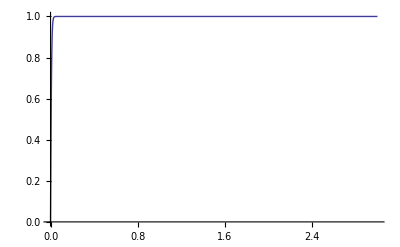

```mathematica
Plot[Tanh[k*100],{k,0,3}]
```

```mathematica
Tdiv[1]
```

FourierSinTransform[(ⅇ^(-k^2) HeavisideTheta[k] Tanh[400. k])/k^8,k,1,FourierParameters→{1,1}]

```mathematica
NIntegrate[P[k]*k^2/k^13*HeavisideTheta[k]*(Tanh[k*umax])*Sin[k*u],{k,0,Infinity}]
```

NIntegrate::inumr: The integrand ⅇ^-k^2\ HeavisideTheta[k]\ Sin[k\ u]\ Tanh[400.\ k]/k^8 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate[(P[k] k^2 HeavisideTheta[k] Tanh[k umax] Sin[k u])/k^13,{k,0,∞}]

```mathematica
Tanh[.00000001]
```

1.×10^-8